# Basic Cosmology

Basic cosmology routines are defined here. These borrow heavily from Hogg, “Distance Measures in Cosmology”.

```mathematica
Needs["Cosmology`Defs`"];
```

## Testing and Examples

```mathematica
CriticalDensity[1.0, FoMSWG]*2
```

2.86919×10^11

```mathematica
CriticalDensity[1.0, FoMSWG]
```

1.43459×10^11

## Power spectrum based tests

Start by reading in a saved power spectrum with sigma8=0.79

```mathematica
pk = Import[FileNameJoin[{NotebookDirectory[], "matterpower.dat"}], "Table"];
```

Set up an interpolating function

```mathematica
pkint = Interpolation[pk, InterpolationOrder->1];
```

InterpolatingFunction::dmval: Input value {-6.90776} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-6.90758} lies outside the range of data in the interpolating function. Extrapolation will be used.

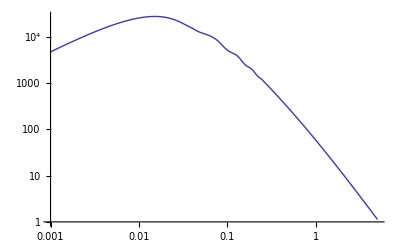

```mathematica
LogLogPlot[pkint[k], {k, 1.*^-3, 5}]
```

```mathematica
Timing[sigmaR[pkint, 8.0, 1.*^-4, 8.0]]
```

{0.1497,0.789882}

We can fiddle around with precision etc -- these are stored in a private variable here.

```mathematica
getOscillatoryIntegralOpts[]
```

{Method→{SymbolicPreprocessing,OscillatorySelection→True,InterpolationPointsSubdivision→False},PrecisionGoal→4,MaxRecursion→20}

```mathematica
setOscillatoryIntegralOpts[{PrecisionGoal->5}]
```

{PrecisionGoal→5,Method→{SymbolicPreprocessing,OscillatorySelection→True,InterpolationPointsSubdivision→False},MaxRecursion→20}

```mathematica
Timing[sigmaR[pkint, 8.0, 1.*^-4, 8.0]]
```

{0.143253,0.789894}

```mathematica
Timing[pk2xi[pkint, 110.0]]
```

{1.18312,0.00158752}

```mathematica
Timing[pk2xi[pkint, 10.0]]
```

{0.252725,0.34248}

```mathematica
Timing[pk2xi[pkint, 200.0]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{1.91312,-0.000159122}

```mathematica
setOscillatoryIntegralOpts[{PrecisionGoal->4}];
```

```mathematica
Timing[pk2xi[pkint, 200.0]]
```

{0.984983,-0.000159124}

```mathematica
Table[{r, r^2*pk2xi[pkint, r]//Quiet}, {r,5.0, 200.0, 3.0}];
```

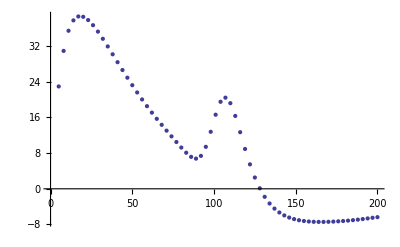

```mathematica
ListPlot[%]
```

Demonstrate that NIntegrate still has the same defaults

```mathematica
Options[NIntegrate]
```

{AccuracyGoal→∞,Compiled→Automatic,EvaluationMonitor→None,Exclusions→None,MaxPoints→Automatic,MaxRecursion→Automatic,Method→Automatic,MinRecursion→0,PrecisionGoal→Automatic,WorkingPrecision→MachinePrecision}